Axicon Gaussian Laser Beams

Kirk T. McDonald, arXiv:0003056v2 (2000)
Notebook: Óscar Amaro, December 2022 @ GoLP-EPP

Introduction
In this notebook we reproduce some results from the paper.

axicon solution for a Gaussian laser beam in vacuum, i.e., a beam with radial polarization of the electric field.

## Figure 2

The electric field Ex(x, 0, z) of a linearly polarized Gaussian beam with diffraction angle θ0 = 0.45, according to eq. (27).
Equation 27 is the definition of W(z) spotsize. Instead, eq 25 is being plotted.

```mathematica
Clear[Ex,E0,rprp,W,W0,g,ϕ,λ,W0,zR,k,z0,x,y,z,ω,t,θ0]
```

(ⅇ^(-(1.99859 (x^2+y^2))/(1+0.404715 z^2)+ⅈ (2 π z (1+(x^2+y^2)/(2 (2.47087+z^2)))-ArcTan[0.636173 z])) E0)/(√(1+0.404715 z^2))

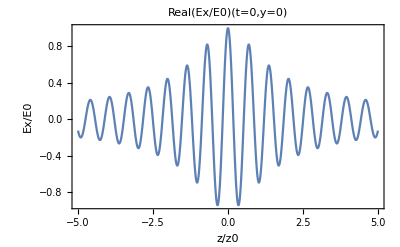

-Graphics3D-

```mathematica
rprp=Sqrt[x^2+y^2];(**)
W=W0 Sqrt[1+z^2/z0^2];(**)
z0=π W0^2/λ;(* Rayleigh range *)
k=2π/λ;
W0=2/(k θ0); (* θ0=2/(k W0) equation 11 *)

(* parameters *)
θ0=0.45;(**)
λ=1;(*[μm]*)
g=1;(* envelope equation...*)
t=0;

(* equation 25 *)
Ex=E0 Exp[-rprp^2/W^2]/Sqrt[1+z^2/z0^2] g Exp[I (k z(1+rprp^2/(2(z^2+z0^2)))-ω t - ArcTan[z/z0])]

(* lineout *)
Plot[Re[Ex/E0]//.{y->0,z->zz0 z0,x->0},{zz0,-5,+5},Frame->True,FrameLabel->{"z/z0","Ex/E0"},PlotLabel->"Real(Ex/E0)(t=0,y=0)"]

(* figure 2 *)
Plot3D[Re[Ex/E0]//.{y->0,z->zz0 z0,x->xW0 W0},{zz0,-5,+5},{xW0,-10,+10},PlotRange->All,PlotPoints->50,Mesh->None,AxesLabel->{"z/z0","x/W0","Ex/E0"},PlotLabel->"Real(Ex/E0)(t=0,y=0)"]
```

## Figure 3

Same as previous figure, but for Ez component

```mathematica
Clear[Ex,E0,rprp,W,W0,g,ϕ,λ,W0,zR,k,z0,x,y,z,ω,t,θ0,Ez,ξ,ζ,f]
```

```mathematica
rprp=Sqrt[x^2+y^2];(**)
W=W0 Sqrt[1+z^2/z0^2];(**)
z0=π W0^2/λ;(* Rayleigh range *)
k=2π/λ;
W0=2/(k θ0); (* θ0=2/(k W0) equation 11 *)

(* parameters *)
θ0=0.45;(**)
λ=1;(*[μm]*)
g=1;(* envelope equation...*)
t=0;

(* eq 12 *)
ξ=x/W0;
ζ=z/z0;

(* eq 19 *)
f=1/(1+I ζ);

(* equation 25 *)
Ex=E0 Exp[-rprp^2/W^2]/Sqrt[1+z^2/z0^2] g Exp[I (k z(1+rprp^2/(2(z^2+z0^2)))-ω t - ArcTan[z/z0])];

Ez = -I θ0 f ξ Ex;

(* figure 3 *)
Plot3D[Re[Ez/E0]//.{y->0,z->zz0 z0,x->xW0 W0},{zz0,-5,+5},{xW0,-10,+10},PlotRange->All,PlotPoints->50,Mesh->None,AxesLabel->{"z/z0","x/W0","Ez/E0"},PlotLabel->"Real(Ez/E0)(t=0,y=0)"]
```

-Graphics3D-

## Figure 4

Lowest-Order Axicon Beam: Er

```mathematica
Clear[Ex,E0,rprp,W,W0,g,ϕ,λ,W0,zR,k,z0,x,y,z,ω,t,θ0,Ez,ξ,ζ,f,ρ,Eprp]
```

```mathematica
rprp=Sqrt[x^2+y^2];(**)
ρ=rprp/W0;(* eq 12 *)
W=W0 Sqrt[1+z^2/z0^2];(**)
z0=π W0^2/λ;(* Rayleigh range *)
k=2π/λ;
W0=2/(k θ0); (* θ0=2/(k W0) equation 11 *)

(* parameters *)
θ0=0.45;(**)
λ=1;(*[μm]*)
g=1;(* envelope equation...*)
t=0;

(* eq 12 *)
ξ=x/W0;
ζ=z/z0;

ϕ=k z + ω t;

(* eq 19 *)
f=1/(1+I ζ);

(* eq 32 *)
Eprp=E0 ρ f^2 Exp[-f ρ^2]g Exp[I ϕ];

(* figure 4 *)
Plot3D[Re[Eprp/E0]//.{y->0,z->zz0 z0,x->xW0 W0},{zz0,-5,+5},{xW0,-10,+10},PlotRange->All,PlotPoints->50,Mesh->None,AxesLabel->{"z/z0","x/W0","E⊥/E0"},PlotLabel->"Real(E⊥/E0)(t=0,y=0)"]
```

-Graphics3D-

## Figure 5

Lowest-Order Axicon Beam: Ez

```mathematica
Clear[Ex,E0,rprp,W,W0,g,ϕ,λ,W0,zR,k,z0,x,y,z,ω,t,θ0,Ez,ξ,ζ,f,ρ,Eprp]
```

```mathematica
rprp=Sqrt[x^2+y^2];(**)
ρ=rprp/W0;(* eq 12 *)
W=W0 Sqrt[1+z^2/z0^2];(**)
z0=π W0^2/λ;(* Rayleigh range *)
k=2π/λ;
W0=2/(k θ0); (* θ0=2/(k W0) equation 11 *)

(* parameters *)
θ0=0.45;(**)
λ=1;(*[μm]*)
g=1;(* envelope equation...*)
t=0;

(* eq 12 *)
ξ=x/W0;
ζ=z/z0;

ϕ=k z + ω t;

(* eq 19 *)
f=1/(1+I ζ);

(* eq 32 *)
Ez=I θ0 E0 f^2(1-f ρ^2)Exp[-f ρ^2]g Exp[I ϕ];

(* figure 5 *)
Plot3D[Re[Ez/E0]//.{y->0,z->zz0 z0,x->xW0 W0},{zz0,-5,+5},{xW0,-10,+10},PlotRange->All,PlotPoints->50,Mesh->None,AxesLabel->{"z/z0","x/W0","Ez/E0"},PlotLabel->"Real(Ez/E0)(t=0,y=0)"]
```

-Graphics3D-